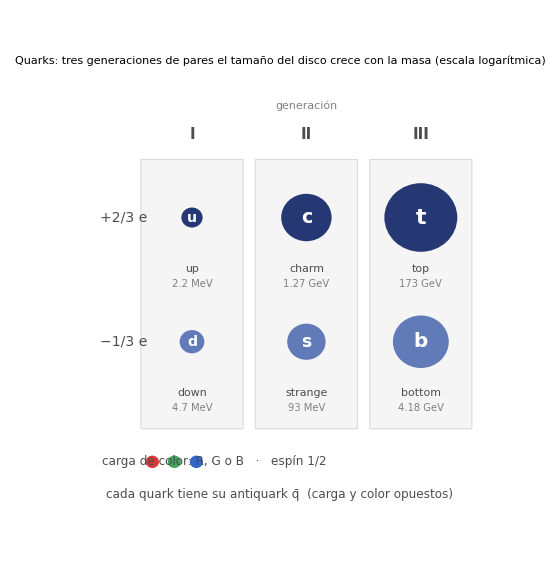

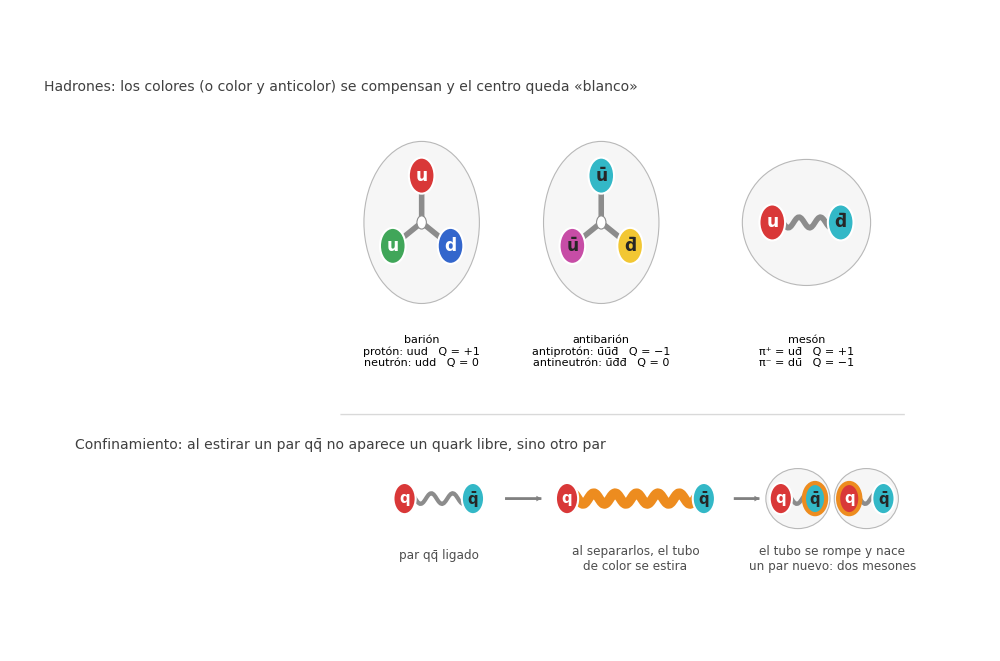

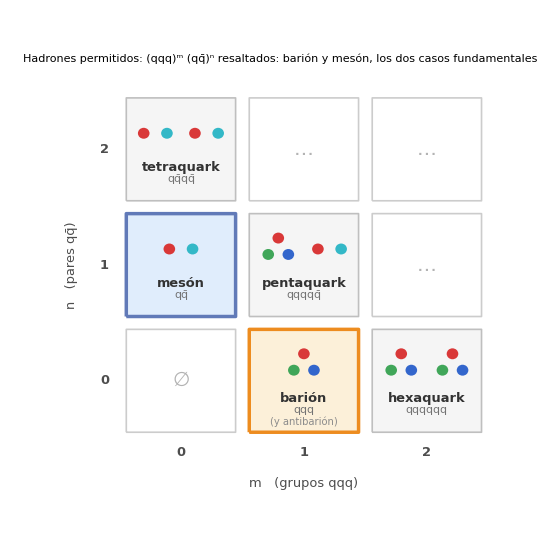

```mathematica
(* ================================================================== *)
(*  QUARKS Y HADRONES                                                  *)
(*  Figura 1: seis sabores en tres generaciones (carga y masa)         *)
(*  Figura 2: hadrones de color neutro y confinamiento                 *)
(*  Figura 3: mapa de hadrones  (qqq)^m (q qbar)^n                     *)
(* ================================================================== *)

ClearAll[mostrarMasas, colR, colG, colB, colAR, colAG, colAB, colUp, colDown, colTubo,
  colTension, quarks, rad, xg, yf, celdaQuark, figQuarks, quarkDisk, halo, tubo,
  barion, meson, leyendaH, yE, rq, paso1, paso2, paso3, flechas, etiq, figHadrones,
  miniB, miniM, nombres, celdaMN, figMapa];

(* ---------- Opción de visualización ---------- *)
mostrarMasas = True;     (* etiquetas numéricas de masa en la figura 1 *)

(* ---------- Paleta ---------- *)
(* carga de color y su anticolor: antirrojo = cian, antiverde = magenta, antiazul = amarillo *)
colR  = RGBColor[0.85, 0.22, 0.22];   colAR = RGBColor[0.20, 0.72, 0.78];
colG  = RGBColor[0.25, 0.65, 0.35];   colAG = RGBColor[0.78, 0.30, 0.65];
colB  = RGBColor[0.20, 0.40, 0.80];   colAB = RGBColor[0.95, 0.78, 0.20];
colUp      = RGBColor[0.15, 0.22, 0.45];   (* quarks tipo up   (carga +2/3) *)
colDown    = RGBColor[0.38, 0.48, 0.72];   (* quarks tipo down (carga -1/3) *)
colTubo    = GrayLevel[0.55];              (* tubo de flujo de color *)
colTension = RGBColor[0.93, 0.55, 0.12];   (* tubo estirado / par creado *)

(* ================================================================== *)
(* FIGURA 1 - Seis sabores de quarks en tres generaciones              *)
(* Tamaño del disco ~ masa (escala logarítmica)                        *)
(* ================================================================== *)
(* {símbolo, nombre, masa aprox. (MeV), etiqueta, fila, generación}
   fila 1 = tipo up (+2/3),  fila 0 = tipo down (-1/3) *)
quarks = {
   {"u", "up",      2.2,      "2.2 MeV",  1, 1},
   {"c", "charm",   1270.,    "1.27 GeV", 1, 2},
   {"t", "top",     173000.,  "173 GeV",  1, 3},
   {"d", "down",    4.7,      "4.7 MeV",  0, 1},
   {"s", "strange", 93.,      "93 MeV",   0, 2},
   {"b", "bottom",  4180.,    "4.18 GeV", 0, 3}};

rad[m_] := 0.10 + 0.06 Log10[m];
xg = {1.3, 2.6, 3.9};     (* centros de las tres generaciones *)
yf = {0, 1.5};            (* filas: down (índice 1) y up (índice 2) *)

celdaQuark[{s_, nom_, m_, et_, f_, g_}] :=
  Module[{x = xg[[g]], y = yf[[f + 1]], c = If[f == 1, colUp, colDown]},
   {{c, Disk[{x, y}, rad[m]]},
    Text[Style[s, Round[10 + 30 rad[m]], Bold, White], {x, y}],
    Text[Style[nom, 11, GrayLevel[0.3]], {x, y - 0.62}],
    If[mostrarMasas, Text[Style[et, 10, GrayLevel[0.5]], {x, y - 0.80}], {}]}];

figQuarks = Graphics[{
    (* fondo de cada generación *)
    {GrayLevel[0.96], EdgeForm[GrayLevel[0.86]],
     Table[Rectangle[{x - 0.58, -1.05}, {x + 0.58, 2.2}, RoundingRadius -> 0.1], {x, xg}]},
    (* cabeceras de columnas y filas *)
    Table[Text[Style[{"I", "II", "III"}[[i]], 15, Bold, GrayLevel[0.3]], {xg[[i]], 2.5}], {i, 3}],
    Text[Style["generación", 11, GrayLevel[0.5]], {xg[[2]], 2.85}],
    Text[Style["+2/3 e", 14, GrayLevel[0.3]], {0.52, yf[[2]]}, {1, 0}],
    Text[Style["−1/3 e", 14, GrayLevel[0.3]], {0.52, yf[[1]]}, {1, 0}],
    (* quarks *)
    celdaQuark /@ quarks,
    (* leyenda: carga de color, espín y antiquarks *)
    MapThread[{#1, Disk[{#2, -1.45}, 0.075]} &, {{colR, colG, colB}, {0.85, 1.1, 1.35}}],
    Text[Style["carga de color: R, G o B   ·   espín 1/2", 12, GrayLevel[0.3]],
     {1.55, -1.45}, {-1, 0}],
    Text[Style[Row[{"cada quark tiene su antiquark ", OverBar["q"], "  (carga y color opuestos)"}],
      12, GrayLevel[0.3]], {2.3, -1.85}]},
   PlotRange -> {{-0.3, 4.9}, {-2.2, 3.15}}, PlotRangePadding -> None,
   ImageSize -> 560,
   PlotLabel -> Column[{Style["Quarks: tres generaciones de pares", 15],
      Style["el tamaño del disco crece con la masa (escala logarítmica)", 11, GrayLevel[0.45]]}, Center]];

(* ================================================================== *)
(* FIGURA 2 - Hadrones de color neutro (arriba) y confinamiento (abajo) *)
(* ================================================================== *)
quarkDisk[pos_, col_, txt_, txtCol_, r_: 0.30, edge_: White] := {
   {col, EdgeForm[{edge, AbsoluteThickness[If[edge === White, 1.5, 3]]}], Disk[pos, r]},
   Text[Style[txt, Round[56 r], Bold, txtCol], pos]};

halo[c_, rr_] := {GrayLevel[0.965], EdgeForm[{GrayLevel[0.72], Dashing[{0.012, 0.012}]}], Disk[c, rr]};

(* tubo de flujo de color entre dos puntos a la misma altura *)
tubo[p1_, p2_, grosor_, col_, amp_: 0.09] :=
  Module[{d = Norm[p2 - p1], n},
   n = Max[2, Round[d/0.04]];
   {col, AbsoluteThickness[grosor], CapForm["Round"],
    Line[Table[p1 + t (p2 - p1) + amp Sin[2 Pi t d/0.5] {0, 1}, {t, 0, 1, 1/n}]]}];

(* barión (o antibarión): tres colores (o anticolores) unidos en un nudo central *)
barion[c_, cols_, letras_, txtCol_] := Module[{v},
   v = Table[c + 0.78 {Cos[a], Sin[a]}, {a, {Pi/2, 7 Pi/6, 11 Pi/6}}];
   {halo[c, 1.35],
    {GrayLevel[0.55], AbsoluteThickness[4], CapForm["Round"], Table[Line[{c, p}], {p, v}]},
    {White, EdgeForm[GrayLevel[0.55]], Disk[c, 0.11]},      (* centro "blanco": color neto nulo *)
    MapThread[quarkDisk[#1, #2, #3, txtCol] &, {v, cols, letras}]}];

(* mesón: color y anticolor unidos por un tubo (aquí π+ = u d̄) *)
meson[c_] := {
   halo[c, {1.5, 1.05}],
   tubo[c + {-0.8, 0}, c + {0.8, 0}, 4, colTubo],
   quarkDisk[c + {-0.8, 0}, colR, "u", White],
   quarkDisk[c + {0.8, 0}, colAR, OverBar["d"], GrayLevel[0.15]]};

leyendaH[titulo_, l1_, l2_] := Column[{Style[titulo, 14, Bold, GrayLevel[0.2]],
    Style[l1, 12, GrayLevel[0.35]], Style[l2, 12, GrayLevel[0.35]]}, Center];

(* --- fila inferior: confinamiento en tres pasos --- *)
yE = -4.6;  rq = 0.26;
paso1 = {tubo[{0, yE}, {1.6, yE}, 3, colTubo],
   quarkDisk[{0, yE}, colR, "q", White, rq],
   quarkDisk[{1.6, yE}, colAR, OverBar["q"], GrayLevel[0.15], rq]};
paso2 = {tubo[{3.8, yE}, {7.0, yE}, 7, colTension],
   quarkDisk[{3.8, yE}, colR, "q", White, rq],
   quarkDisk[{7.0, yE}, colAR, OverBar["q"], GrayLevel[0.15], rq]};
paso3 = {halo[{9.2, yE}, {0.75, 0.5}], halo[{10.8, yE}, {0.75, 0.5}],
   tubo[{8.8, yE}, {9.6, yE}, 3, colTubo], tubo[{10.4, yE}, {11.2, yE}, 3, colTubo],
   quarkDisk[{8.8, yE}, colR, "q", White, rq],
   quarkDisk[{9.6, yE}, colAR, OverBar["q"], GrayLevel[0.15], rq, colTension],   (* par nuevo *)
   quarkDisk[{10.4, yE}, colR, "q", White, rq, colTension],                      (* par nuevo *)
   quarkDisk[{11.2, yE}, colAR, OverBar["q"], GrayLevel[0.15], rq]};
flechas = {GrayLevel[0.5], AbsoluteThickness[2], Arrowheads[0.018],
   Arrow[{{2.35, yE}, {3.2, yE}}], Arrow[{{7.7, yE}, {8.3, yE}}]};
etiq = {
   Text[Style[Row[{"par ", "q", OverBar["q"], " ligado"}], 12, GrayLevel[0.3]], {0.8, yE - 0.95}],
   Text[Style[Column[{"al separarlos, el tubo", "de color se estira"}, Center], 12, GrayLevel[0.3]],
    {5.4, yE - 1.0}],
   Text[Style[Column[{"el tubo se rompe y nace", "un par nuevo: dos mesones"}, Center], 12, GrayLevel[0.3]],
    {10.0, yE - 1.0}]};

figHadrones = Graphics[{
    Text[Style["Hadrones: los colores (o color y anticolor) se compensan y el centro queda «blanco»",
      14, GrayLevel[0.25]], {-1.5, 2.25}, {-1, 0}],
    barion[{0.4, 0}, {colR, colG, colB}, {"u", "u", "d"}, White],
    barion[{4.6, 0}, {colAR, colAG, colAB}, {OverBar["u"], OverBar["u"], OverBar["d"]}, GrayLevel[0.15]],
    meson[{9.4, 0}],
    Text[leyendaH["barión", "protón: uud   Q = +1", "neutrón: udd   Q = 0"], {0.4, -2.15}],
    Text[leyendaH["antibarión",
      Row[{"antiprotón: ", OverBar["u"], OverBar["u"], OverBar["d"], "   Q = −1"}],
      Row[{"antineutrón: ", OverBar["u"], OverBar["d"], OverBar["d"], "   Q = 0"}]], {4.6, -2.15}],
    Text[leyendaH["mesón",
      Row[{Superscript["π", "+"], " = u", OverBar["d"], "   Q = +1"}],
      Row[{Superscript["π", "−"], " = d", OverBar["u"], "   Q = −1"}]], {9.4, -2.15}],
    {GrayLevel[0.85], AbsoluteThickness[1], Line[{{-1.5, -3.2}, {11.7, -3.2}}]},
    Text[Style[Row[{"Confinamiento: al estirar un par q", OverBar["q"],
        " no aparece un quark libre, sino otro par"}], 14, GrayLevel[0.25]], {-1.5, -3.7}, {-1, 0}],
    paso1, paso2, paso3, flechas, etiq},
   PlotRange -> {{-1.7, 11.9}, {-6.3, 2.7}}, PlotRangePadding -> None, ImageSize -> 1000];

(* ================================================================== *)
(* FIGURA 3 - Mapa de hadrones  (qqq)^m (q qbar)^n  con m + n <= 2     *)
(* ================================================================== *)
miniB[c_] := MapThread[{#2, Disk[c + 0.17 {Cos[#1], Sin[#1]}, 0.085]} &,
   {{Pi/2, 7 Pi/6, 11 Pi/6}, {colR, colG, colB}}];
miniM[c_] := {{colR, Disk[c + {-0.17, 0}, 0.085]}, {colAR, Disk[c + {0.17, 0}, 0.085]}};

nombres = <|{1, 0} -> "barión", {0, 1} -> "mesón", {2, 0} -> "hexaquark",
   {1, 1} -> "pentaquark", {0, 2} -> "tetraquark"|>;

celdaMN[m_, n_] := Module[{c = 1.8 {m, n}, k = m + n, items, xs, fondo, borde, grosor},
   If[k == 0 || k > 2,
    (* vacío (m = n = 0) o combinaciones mayores *)
    {FaceForm[None], EdgeForm[{GrayLevel[0.8], AbsoluteThickness[1.2], Dashing[{0.015, 0.015}]}],
     Rectangle[c - {0.8, 0.8}, c + {0.8, 0.8}, RoundingRadius -> 0.1],
     Text[Style[If[k == 0, "∅", "…"], 20, GrayLevel[0.7]], c]},
    items = Join[ConstantArray["B", m], ConstantArray["M", n]];
    xs = c[[1]] + 0.75 (Range[k] - (k + 1)/2);
    fondo = Which[{m, n} == {1, 0}, RGBColor[0.99, 0.94, 0.85],
      {m, n} == {0, 1}, RGBColor[0.88, 0.93, 0.99], True, GrayLevel[0.96]];
    borde = Which[{m, n} == {1, 0}, colTension, {m, n} == {0, 1}, colDown, True, GrayLevel[0.75]];
    grosor = If[k == 1, 2.5, 1.2];
    {{fondo, EdgeForm[{borde, AbsoluteThickness[grosor]}],
      Rectangle[c - {0.8, 0.8}, c + {0.8, 0.8}, RoundingRadius -> 0.1]},
     MapThread[If[#1 == "B", miniB[{#2, c[[2]] + 0.25}], miniM[{#2, c[[2]] + 0.25}]] &, {items, xs}],
     Text[Style[nombres[{m, n}], 13, Bold, GrayLevel[0.2]], c + {0, -0.28}],
     Text[Style[Row[Join[ConstantArray["qqq", m], ConstantArray[Row[{"q", OverBar["q"]}], n]], "  "],
       11, GrayLevel[0.45]], c + {0, -0.46}],
     If[{m, n} == {1, 0}, Text[Style["(y antibarión)", 10, GrayLevel[0.55]], c + {0, -0.64}], {}]}]];

figMapa = Graphics[{
    Table[celdaMN[m, n], {m, 0, 2}, {n, 0, 2}],
    (* ejes *)
    Table[Text[Style[ToString[m], 13, Bold, GrayLevel[0.3]], {1.8 m, -1.12}], {m, 0, 2}],
    Table[Text[Style[ToString[n], 13, Bold, GrayLevel[0.3]], {-1.12, 1.8 n}], {n, 0, 2}],
    Text[Style[Row[{"m   (grupos qqq)"}], 13, GrayLevel[0.3]], {1.8, -1.6}],
    Text[Style[Row[{"n   (pares q", OverBar["q"], ")"}], 13, GrayLevel[0.3]], {-1.6, 1.8}, {0, 0}, {0, 1}]},
   PlotRange -> {{-1.9, 4.8}, {-2.0, 4.7}}, PlotRangePadding -> None, ImageSize -> 560,
   PlotLabel -> Column[{
      Style[Row[{"Hadrones permitidos:  ", Superscript["(qqq)", "m"], " ",
         Superscript[Row[{"(q", OverBar["q"], ")"}], "n"]}], 15],
      Style["resaltados: barión y mesón, los dos casos fundamentales", 11, GrayLevel[0.45]]}, Center]];

(* ---------- Mostrar ---------- *)
Print[figQuarks]; Print[figHadrones]; Print[figMapa];

(* Exportar (opcional):
   SetDirectory[NotebookDirectory[]];
   Export["quarks_sabores.png",  figQuarks,    ImageResolution -> 300];
   Export["hadrones_color.png",  figHadrones,  ImageResolution -> 300];
   Export["hadrones_mapa.png",   figMapa,      ImageResolution -> 300];
*)
```